```mathematica
(*range of values for inclination angle of northern wing*)
RE= 1353 * 10^3;(*moon radius in m*)
B0= 5.1369 * 10^-9; (*background field magnitude in T*)
B0x=0;
B0y=0;
B0z=-B0;  (*background magnetic field in system (x,y,z)*)

n0=0.11 * 10^6; (*upstream number density in 1/m^3*)
u0=43*10^3; (*magnitude of upstream flow velocity in m/s*)
u0xcor=u0;
u0ycor=0;
u0zcor=0; (*upstream flow velocity in system (xcor,ycor,zcor)*)
E0norm= u0*B0; (*may be needed for normalization purposes*)
mp=1.6726231*10^-27; (*proton mass*)
m=7.5 * mp; (*upstream ion mass*)
mu0= 4 * 3.14159265359* 10^-7; (*magnetic permeability of vacuum*)

vA=B0/(√(mu0 * n0 * m)); (*Alfven velocity*)
MA= u0/vA (*Alfvenic Mach number*)
ThetaN[theta_]=ArcTan[(MA Cos[theta])/(1-MA Sin[theta])] *360/(2 π);
ThetaS[theta_]=ArcTan[(MA Cos[theta])/(1+MA Sin[theta])] *360/(2 π);(*inclination angle against B0 for NORTHERN Alfven wing*)
```

0.348577

```mathematica
(*tilt of flow vector in northern and southern wing against x axis for fully saturated case*)
flowtiltN[theta_]=Tan[(90+ThetaN[theta*(2 Pi)/360]-theta)*(2 Pi)/360];
flowtiltS[theta_]=Tan[(90-ThetaS[theta*(2 Pi)/360]-theta)*(2 Pi)/360];
```

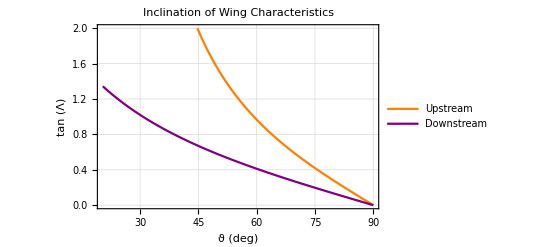

```mathematica
Plot4=Plot[{flowtiltN[theta],flowtiltS[theta]},{theta, ArcSin[MA]*360/(2π), 90}, FrameLabel->{"ϑ (deg)","tan (Λ)"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"Inclination of Wing Characteristics", PlotStyle->{{Orange,Thick},{Purple,Thick}},  PlotLegends ->{"Upstream","Downstream"},PlotRange->{0,2}]
```

```mathematica
Export["figure4.pdf",Plot4]
```

figure4.pdf